## Snowball

```mathematica
r[t_]=-1/((-1/3) t-1/2)
```

-1/(-1/2-t/3)

```mathematica
Simplify[-1/(-1/2-t/3)]
```

6/(3+2 t)

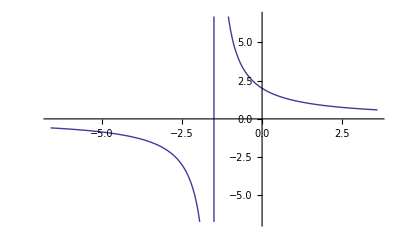

```mathematica
Plot[6/(3+2 t),{t,-6.6,3.6}]
```

```mathematica
Solve[r[t]==.1,t]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→28.5}}

```mathematica
r[3/2]
```

1

## Fish

```mathematica
.2/(4*10^(-5))
```

5000.

```mathematica
.2/5000
```

0.00004

```mathematica
1000*4000*4/100000
```

160

```mathematica
DSolve[{P'[t]==.2 P[t]-4*10^(-5)P[t]^2,P[0]==1000},P[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P[t]→(5000. 2.71828^(0.2 t))/(4.+2.71828^(0.2 t))}}

```mathematica
{{P[t]->(5000. 2.718281828459045^(0.2 t))/(4.+2.718281828459045^(0.2 t))}}⟦1,1,2⟧
```

(5000. 2.71828^(0.2 t))/(4.+2.71828^(0.2 t))

```mathematica
p[t_]=(5000. 2.718281828459045^(0.2 t))/(49.00000000000001+2.718281828459045^(0.2 t))
```

(5000. 2.71828^(0.2 t))/(49.+2.71828^(0.2 t))

```mathematica
p'[0]
```

19.6

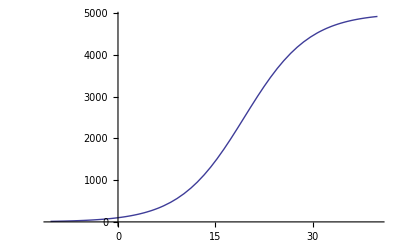

```mathematica
Plot[(5000. 2.718281828459045^(0.2 t))/(49.00000000000001+2.718281828459045^(0.2 t)),{t,-10.39720770839918,40}]
```

## Predator-Prey